Last modified on: Monday, July 9, 2018 at 15:03

Author Info

Enrico Castro Grespan

Grankovsky Vladimir

IER-UNAM

Poster Session Content

Rooftop Recognition for Solar Energy Potential

The aim of this project is to detect the rooftop of buildings to determine the available area at different locations and to identify the most suitable ones for solar energy application such as solar PV using Neural Networks and satellite imagery.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics--Graphics-

A neural net was trained and tested using a dataset which contained the aerial images of five different cities and their corresponding mask. A mask is a binary image where white pixels tell us where are the building rooftops and a black pixel for the rest of the image. A generator function to load a batch of files into the training was needed to handle the whole dataset. The neural net to trained was chosen from the Semantic Segmentation category at Wolfram Neural Net Repository. “Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data” net was modify for the specific needs of the dataset and the classes to return. A good correlation between the test images and their rooftops was obtained.

- Superpose the solar radiation map for solar thermal or PV applications.
- Calculate the ground area of the rooftops.
- Train with high resolution images and masks of other regions of interest.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

The Dataset

Type text hereAmount: 180 
Size: 5000x5000 
Resolution: 30 cm
Ground truth data for two semantic classes : building and not building

-Graphics-

The net

NetGraph[<>]

Generator

In order to train the net with a big amount of data a generator function was created. The generator function load a single batch of data from an external source to train each time.

partGenerator=Function[Block[{batch,dataSet,batchData},
	If[!ValueQ[partitionedData],partitionedData=Partition[Range[Length[data]],#BatchSize,#BatchSize,1]];
	Print[Association@Thread[Keys[#]→Values[#]]];
	batch=Mod[#AbsoluteBatch,Floor[Length@data/#BatchSize]];
	batchData=data⟦partitionedData[[Echo@(batch+1)]]⟧;
	
	Thread[Keys[batchData]→1+BinaryDeserialize/@Values[batchData]]
]
];

Results

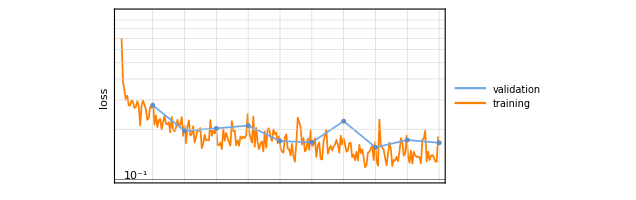
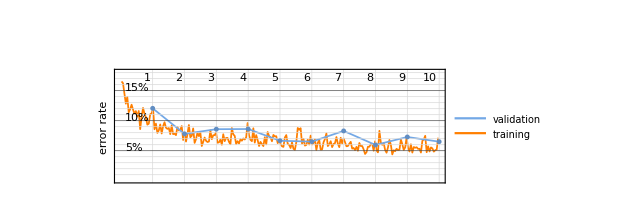

-Graphics--Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

Provide one of:

Link to the GitHub

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

https://project.inria.fr/aerialimagelabeling/

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

Neural Networks

Semantic Segmentation

Solar Energy

#### Other information